# Graph Complexity

## Program

```mathematica
graphRedundancyComplexity[g_Graph]:=Module[{vc,ec,ecmean,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
ecmean = ec/(vc^2);
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
(vc) (vc^ecmean) Exp[etp]
]
```

```mathematica
graphComplexity[g_Graph]:=Module[{vc,ec,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
vc^2 ec etp
]
```

```mathematica
graphComplexityE[g_Graph]:=Module[{vc,ec,etp},
(*vc=VertexCount[g]//N;*)
ec=EdgeCount[g]//N;
(*etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;*)
etp=Entropy[Map[#[[2]]&,Tally[EdgeList[g]]]]//N;
vc^2 ec etp
]
```

```mathematica
graphComplexityD[g_Graph]:=Module[{ec,etp,vc,vinetp,voutetp},
ec=EdgeCount[g]//N;
vc=VertexCount[g]//N;
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
vinetp=Entropy[VertexInDegree[g]]//N;
voutetp=Entropy[VertexOutDegree[g]]//N;
ec etp vc vinetp vc voutetp
]
```

```mathematica
graphComplexityDp[g_Graph]:=Module[{ec,etp,vc,vinetp,voutetp},
ec=EdgeCount[g]//N;
vc=VertexCount[g]//N;
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
vinetp=Entropy[VertexInDegree[g]]//N;
voutetp=Entropy[VertexOutDegree[g]]//N;
ec^etp vc^vinetp vc^voutetp
]
```

## Test

### Graph

```mathematica
cg3=Graph[{1->1,1->2,1->3,2->1,2->2,2->3,3->1,3->2,3->3}]
```

-Graphics-

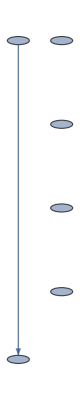

```mathematica
g0=Graph[{1,2,3,4,5,6},{5->6}]
```

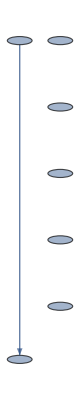

```mathematica
g0v=Graph[{1,2,3,4,5,6,7},{5->6}]
```

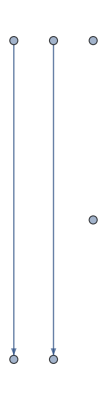

```mathematica
g0e=Graph[{1,2,3,4,5,6},{5->6,1->2}]
```

```mathematica
g=Graph[{1->2,2->3,3->4,2->1,3->4}]
```

-Graphics-

```mathematica
g2=Graph[{1,2,3},{}]
```

-Graphics-



```mathematica
g3=Graph[{1,2,3},{1->2,2->3,3->1}]
```

### Test

```mathematica
graphRedundancyComplexity[g0]
graphRedundancyComplexity[g0v]
graphRedundancyComplexity[g0e]
```

7.15965

8.04657

8.21417

```mathematica
graphRedundancyComplexity[cg3]
```

9.

```mathematica
graphRedundancyComplexity[g3]
```

8.17704

```mathematica
graphRedundancyComplexity[g2]
```

3.

```mathematica
graphComplexity[g]
```

56.2335

```mathematica
graphComplexityD[g]
```

32.8781

```mathematica
graphComplexityDp[g]
```

28.5662

```mathematica
graphComplexity[g2]
```

0.

```mathematica
graphComplexityD[g2]
```

0.

```mathematica
graphComplexityDp[g2]
```

Power::indet: Indeterminate expression 0.^0. encountered.

Indeterminate

```mathematica
graphComplexity[g3]
```

17.1859

```mathematica
graphComplexityD[g3]
```

0.

```mathematica
graphComplexityDp[g3]
```

2.01231

```mathematica
graphComplexity[g0]
graphComplexity[g0v]
graphComplexity[g0e]
```

4.5695

4.88155

15.4483

```mathematica
graphComplexityE[g0]
graphComplexityE[g0v]
graphComplexityE[g0e]
```

0.

0.

0.

```mathematica
graphComplexityD[g0]
graphComplexityD[g0v]
graphComplexityD[g0e]
```

0.927633

0.821054

6.25887

```mathematica
graphComplexityDp[g0]
graphComplexityDp[g0v]
graphComplexityDp[g0e]
```

5.02585

4.93375

11.3553

```mathematica
g0
```

-Graphics-

```mathematica
AdjacencyMatrix[g0]//Flatten//Normal//Entropy//N
```

0.126931

```mathematica
VertexInDegree[g0]//Entropy//N
```

0.450561

```mathematica
Entropy[{0,0,0,1}]//N
Entropy[{1,1,0,1}]//N
Entropy[{0,0,0,1,0}]//N
```

0.562335

0.562335

0.500402

```mathematica
Entropy[2,{0,0,0,1}]//N
Entropy[2,{1,1,0,1}]//N
Entropy[2,{0,0,0,1,0}]//N
```

0.811278

0.811278

0.721928

```mathematica
scaleEntropy[l_]:=Module[{mean},
mean=Mean[l];
Entropy[l]*mean
]
```

```mathematica
totalEntropy[l_]:=Module[{total},
total=Total[l];
total^Entropy[l]
]
```

```mathematica
scaleEntropy[{0,0,0,1}]//N
scaleEntropy[{1,1,0,1}]//N
scaleEntropy[{0,0,0,1,0}]//N
```

0.140584

0.421751

0.10008

```mathematica
totalEntropy[{0,0,0,1}]//N
totalEntropy[{1,1,0,1}]//N
totalEntropy[{0,0,0,1,0}]//N
```

1.

1.85482

1.

```mathematica
graphComplexityE[g3]
```

0.

## Memo

```mathematica
Entropy[{1,2,3}]
```

Log[3]

```mathematica
Exp[Entropy[{1,2,3}]]//N
```

3.

```mathematica
cg3//AdjacencyMatrix//Normal
```

{{0,1,1},{1,0,1},{1,1,0}}